Wolfram Online Mini Campus. Part 18

Instagram Posts
Pinterest Posts
"Translation" of  :d83d:dcd1  SageMath Online Mini Campus. Part 18
http://www.wolfram.com/broadcast/video.php?c=460&v=2665

Exercises with Representation Options

```mathematica
PopupView[ExampleData["Classes"]]
SlideView[ExampleData["Geometry3D"]]
```

```mathematica
MenuView[(# ->GraphData[#])&/@Take[GraphData["Hypercube"],5],Background->LightGreen]
```

```mathematica
TabView[(# ->ExampleData[#])&/@Take[ExampleData["Geometry3D"],3]]
```

123

```mathematica
RandomInstance[GeometricScene[{A1,B1,C1,O1},
{T1==Triangle[{A1,B1,C1}],CircleThrough[{A1,B1,C1},O1],
O1==TriangleCenter[T1,"Centroid"]}]]
```

-Graphics-

Exercises with Dataset Options

data=Import[StringJoin[user,"c_bank.csv"],{"CSV","Dataset"},"HeaderLines"→1,
"DateStringFormat"→{"Year","-","Month","-","Day"}];

```mathematica
user="https://olgabelitskaya.github.io/"; 
data=SemanticImport[StringJoin[user,"c_bank.csv"]];
dataF=Table[DateList[DateObject[data[[i,1]]]][[1;;3]],{i,Length[data]}];
dataG=Dataset[Table[{dataF[[i]],data[[i,4]]},{i,Length[data]}]];
dataP=Dataset[Table[{dataF[[i]],data[[i,6]]},{i,Length[data]}]];
```

```mathematica
DateListLogPlot[data[[All,{1,4}]],{{2012,1,1},{2012,4,30}},Frame->True,Filling->Axis]
```

-Graphics-

```mathematica
KagiChart[data[[All,{1,5}]]]
```

-Graphics-

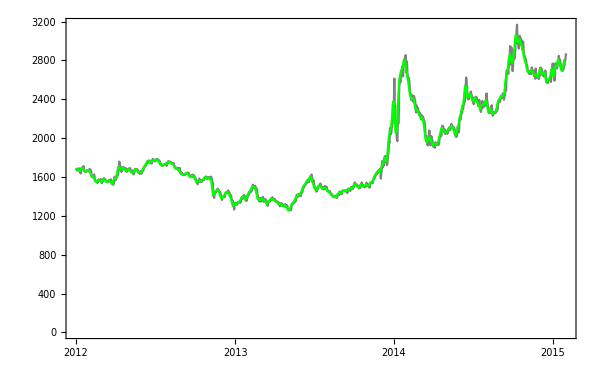

```mathematica
DateListPlot[{data[[All,4]],MovingAverage[Normal[data[[All,4]]],5]},{2012,1,1},
PlotStyle->{Gray,Green},ImageSize->{600,400}]
```

```mathematica
tem=Import["ExampleData/temperatures.json"];
DateListPlot[Table[{DateList[DateObject[StringJoin["20",StringTake[Keys[tem][[i]],7;;8],
StringTake[Keys[tem][[i]],1;;2],StringTake[Keys[tem][[i]],4;;5]],
   DateFormat->{"Year","/","Month","/","Day"}]][[1;;3]],
Values[tem[[i]]]},{i,31}],ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
path="https://data.cityofnewyork.us/resource/";
SE=Import[StringJoin[path,"h7rb-945c.json"],HeaderLines->1];
FL=Keys[SE][[1,{1,26,75,79,80,82,34,35}]]
Table[Values[SE[[i,{1,26,75,79,80,82,34,35}]]],{i,1}]
```

{dbn,total_students,city,latitude,longitude,council_district,graduation_rate,attendance_rate}

{{08X519,242,Bronx,40.820486,-73.881187,17,0.49,0.81}}

Exercises with Surfaces

```mathematica
RP[a_]:=RevolutionPlot3D[{u^3,Cos[a*u],2u^2},{u,0,1},{phi,0,2Pi},
ColorFunction->Function[{x,y,z},ColorData["DeepSeaColors"][Cos[169x+144y+121z]]],
PlotRange->{{-1.5,1.5},{-1.5,1.5},{0,2}},PlotPoints->150,PlotStyle->Opacity[.7],
Mesh->False,Axes->False,Boxed->False,ImageSize->Large];
RP[8]
```

-Graphics3D-

Exercises with Functions

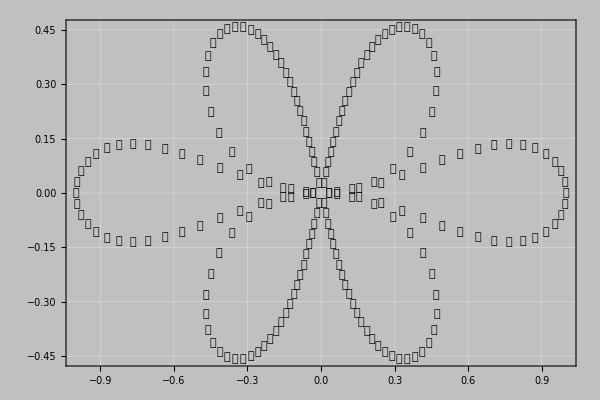

```mathematica
v=Table[{1/Cos[-Pi/2+3Pi*i/100],Tan[-Pi/2+Pi*i/100]},
{i,Join[Range[1,99,1],Range[101,199,1]]}];
L=Table [{v[[i,1]]/(v[[i,1]]^2+v[[i,2]]^2), v[[i,2]]/(v[[i,1]]^2+v[[i,2]]^2)},{i,198}];
Graphics[Table[Style[Text[CharacterRange["砀","礀"][[i]],L[[i]]],12,Hue[i/200]],{i,198}],
ImageSize->{600,400},AspectRatio->2/3,Frame->True,
GridLines->Automatic,Background->RGBColor["silver"]]
```

```mathematica
PolarPlot[{Cos[12θ],1+Cos[12θ]},{θ,0,2Pi},PlotStyle->{Red,Blue}]
```

-Graphics-

Exercises with HTML & CSS

```mathematica
EmbeddedHTML["<div id='test_highcharts' style='width:300px; height:400px;'></div>
<script src='https://code.highcharts.com/highcharts.js'></script><script>
var xy1=Array(640).fill(0).map((r,t)=>[((r+Math.cos(0.12*t))*Math.cos(0.01*t)),
                                 ((r+Math.cos(0.12*t))*Math.sin(0.01*t))]);
var xy2=Array(640).fill(1).map((r,t)=>[((r+Math.cos(0.12*t))*Math.cos(0.01*t)),
                                 ((r+Math.cos(0.12*t))*Math.sin(0.01*t))]);
Highcharts.chart('test_highcharts', {
    chart:{type:'area'},xAxis:{title:{text:'x'}},yAxis:{title:{text:'y'}},
    title:{text:'Parametric Area Plot'},credits:{enabled:false},
    series: [{name:'ϱ = cos 12 θ',color:'#ff3636',data:xy1},
           {name:'ϱ = 1 + cos 12 θ',color:'#3636ff',data:xy2}]
});</script>",ImageSize->{350,450}]
```

Null«781»<div id='test_highcharts' style='width:300px; height:400px;'></div>
<script src='https://code.highcharts.com/highcharts.js'></script><script>
var xy1=Array(640).fill(0).map((r,t)=>[((r+Math.cos(0.12*t))*Math.cos(0.01*t)),
                                 ((r+Math.cos(0.12*t))*Math.sin(0.01*t))]);
var xy2=Array(640).fill(1).map((r,t)=>[((r+Math.cos(0.12*t))*Math.cos(0.01*t)),
                                 ((r+Math.cos(0.12*t))*Math.sin(0.01*t))]);
Highcharts.chart('test_highcharts', {
    chart:{type:'area'},xAxis:{title:{text:'x'}},yAxis:{title:{text:'y'}},
    title:{text:'Parametric Area Plot'},credits:{enabled:false},
    series: [{name:'ϱ = cos 12 θ',color:'#ff3636',data:xy1},
           {name:'ϱ = 1 + cos 12 θ',color:'#3636ff',data:xy2}]
});</script>

```mathematica
EmbeddedHTML["
<div id='test_googlechart' style='width:400px;height:400px;'></div>
<script src='https://www.gstatic.com/charts/loader.js'></script><script>
google.charts.load('current',{'packages':['corechart']}); 
google.charts.setOnLoadCallback(drawChart);
function drawChart() {
    var xy=Array(1274).fill(0).map((r,t)=>[(Math.floor(t/638)+r+Math.cos(0.12*t))*Math.cos(0.01*t),
                                     (r+Math.cos(0.12*t))*Math.sin(0.01*t),
                                     (r+1+Math.cos(0.12*t))*Math.sin(0.01*t)]);
    for (var i=1; i<637; i++) {xy[637+i][1]=NaN; xy[i+1][2]=NaN;}; 
    xy.unshift(['x','ϱ = cos 12θ','ϱ = 1 + cos 12θ']); 
    var data=google.visualization.arrayToDataTable(xy); 
    var options={curveType:'function',legend:{position:'bottom'}};
    var chart=new google.visualization.LineChart(document.getElementById('test_googlechart')); 
    chart.draw(data,options);
};</script>",ImageSize->{420,420}]
```

Null«926»
<div id='test_googlechart' style='width:400px;height:400px;'></div>
<script src='https://www.gstatic.com/charts/loader.js'></script><script>
google.charts.load('current',{'packages':['corechart']}); 
google.charts.setOnLoadCallback(drawChart);
function drawChart() {
    var xy=Array(1274).fill(0).map((r,t)=>[(Math.floor(t/638)+r+Math.cos(0.12*t))*Math.cos(0.01*t),
                                     (r+Math.cos(0.12*t))*Math.sin(0.01*t),
                                     (r+1+Math.cos(0.12*t))*Math.sin(0.01*t)]);
    for (var i=1; i<637; i++) {xy[637+i][1]=NaN; xy[i+1][2]=NaN;}; 
    xy.unshift(['x','ϱ = cos 12θ','ϱ = 1 + cos 12θ']); 
    var data=google.visualization.arrayToDataTable(xy); 
    var options={curveType:'function',legend:{position:'bottom'}};
    var chart=new google.visualization.LineChart(document.getElementById('test_googlechart')); 
    chart.draw(data,options);
};</script>

```mathematica
EmbeddedHTML["<table style='width:75%; background-color:slategray; font-size:140%;'>
    <tr><th>Crayola Fluorescent Colors</th><th>Hex</th></tr>
    <tr><td style='background-color:#FF355E;'>Radical Red</td><td style='color:#FF355E;'><center>&#35;FF355E</center></td></tr>
    <tr><td style='background-color:#FD5B78;'>Wild Watermelon</td><td style='color:#FD5B78;'><center>&#35;FD5B78</center></td></tr>
    <tr><td style='background-color:#FF6037;'>Outrageous Orange</td><td style='color:#FF6037;'><center>&#35;FF6037</center></td></tr>
    <tr><td style='background-color:#FF9966;'>Atomic Tangerine</td><td style='color:#FF9966;'><center>&#35;FF9966</center></td></tr>
    <tr><td style='background-color:#FF9933;'>Neon Carrot</td><td style='color:#FF9933;'><center>&#35;FF9933</center></td></tr>
    <tr><td style='background-color:#FFCC33;'>Sunglow</td><td style='color:#FFCC33;'><center>&#35;FFCC33</center></td></tr>    
    <tr><td style='background-color:#FFFF66;'>Laser Lemon</td><td style='color:#FFFF66;'><center>&#35;FFFF66</center></td></tr>
    <tr><td style='background-color:#CCFF00;'>Electric Lime</td><td style='color:#CCFF00;'><center>&#35;CCFF00</center></td></tr>
    <tr><td style='background-color:#66FF66;'>Screamin&#39; Green</td><td style='color:#66FF66;'><center>&#35;66FF66</center></td></tr>
    <tr><td style='background-color:#AAF0D1;'>Magic Mint</td><td style='color:#AAF0D1;'><center>&#35;AAF0D1</center></td></tr>
    <tr><td style='background-color:#50BFE6;'>Blizzard Blue</td><td style='color:#50BFE6;'><center>&#35;50BFE6</center></td></tr>
    <tr><td style='background-color:#FF6EFF;'>Shocking Pink</td><td style='color:#FF6EFF;'><center>&#35;FF6EFF</center></td></tr>
    <tr><td style='background-color:#EE34D2;'>Razzle Dazzle Rose</td><td style='color:#EE34D2;'><center>&#35;EE34D2</center></td></tr>
    <tr><td style='background-color:#FF00CC;'>Hot Magenta</td><td style='color:#FF00CC;'><center>&#35;FF00CC</center></td></tr>
</table>",ImageSize->{600,500}]
```

Null<table style='width:75%; background-…5;FF00CC</center></td></tr>
</table><table style='width:75%; background-color:slategray; font-size:140%;'>
    <tr><th>Crayola Fluorescent Colors</th><th>Hex</th></tr>
    <tr><td style='background-color:#FF355E;'>Radical Red</td><td style='color:#FF355E;'><center>&#35;FF355E</center></td></tr>
    <tr><td style='background-color:#FD5B78;'>Wild Watermelon</td><td style='color:#FD5B78;'><center>&#35;FD5B78</center></td></tr>
    <tr><td style='background-color:#FF6037;'>Outrageous Orange</td><td style='color:#FF6037;'><center>&#35;FF6037</center></td></tr>
    <tr><td style='background-color:#FF9966;'>Atomic Tangerine</td><td style='color:#FF9966;'><center>&#35;FF9966</center></td></tr>
    <tr><td style='background-color:#FF9933;'>Neon Carrot</td><td style='color:#FF9933;'><center>&#35;FF9933</center></td></tr>
    <tr><td style='background-color:#FFCC33;'>Sunglow</td><td style='color:#FFCC33;'><center>&#35;FFCC33</center></td></tr>    
    <tr><td style='background-color:#FFFF66;'>Laser Lemon</td><td style='color:#FFFF66;'><center>&#35;FFFF66</center></td></tr>
    <tr><td style='background-color:#CCFF00;'>Electric Lime</td><td style='color:#CCFF00;'><center>&#35;CCFF00</center></td></tr>
    <tr><td style='background-color:#66FF66;'>Screamin&#39; Green</td><td style='color:#66FF66;'><center>&#35;66FF66</center></td></tr>
    <tr><td style='background-color:#AAF0D1;'>Magic Mint</td><td style='color:#AAF0D1;'><center>&#35;AAF0D1</center></td></tr>
    <tr><td style='background-color:#50BFE6;'>Blizzard Blue</td><td style='color:#50BFE6;'><center>&#35;50BFE6</center></td></tr>
    <tr><td style='background-color:#FF6EFF;'>Shocking Pink</td><td style='color:#FF6EFF;'><center>&#35;FF6EFF</center></td></tr>
    <tr><td style='background-color:#EE34D2;'>Razzle Dazzle Rose</td><td style='color:#EE34D2;'><center>&#35;EE34D2</center></td></tr>
    <tr><td style='background-color:#FF00CC;'>Hot Magenta</td><td style='color:#FF00CC;'><center>&#35;FF00CC</center></td></tr>
</table>